```mathematica
Integrate[Sin[x]Sin[2x],x]
```

Sin[x]/2-1/6 Sin[3 x]

```mathematica
U={{1,-1},{1,1}}
```

```mathematica
ArcTan[2*3.484/7.351]
```

0.758657

```mathematica
N[0.7586568615210438/°]
```

43.4678

```mathematica
gammaS =7.351*10^(-12);
gammaL=1.287*10^(-14);
deltam=3.484*10^(-12);
epsilon=2.228*10^(-3);
phi=0.7586568615210438;
reEps=epsilon*Cos[phi];
Cplus[t_]:=Exp[-gammaS*t]+Exp[-gammaL*t]+2*Exp[-0.5*(gammaS+gammaL)*t]*Cos[deltam*t];
Cminus[t_]:=Exp[-gammaS*t]+Exp[-gammaL*t]-2*Exp[-0.5*(gammaS+gammaL)*t]*Cos[deltam*t];

nplus[t_]:=Cplus[t]*(1+2*reEps);
nminus[t_]:=Cminus[t]*(1-2*reEps);
asymmetry[t_]:=(nplus[t]-nminus[t])/(nplus[t]+nminus[t]);
```

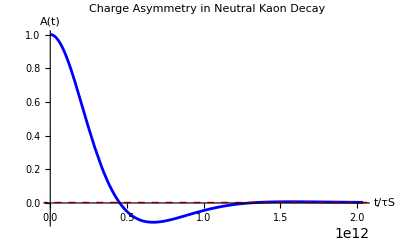

```mathematica
tauS=1/gammaS;
Plot[asymmetry[t],{t,0,15*tauS},PlotRange->All,AxesLabel->{"t/τS","A(t)"},PlotLabel->"Charge Asymmetry in Neutral Kaon Decay",GridLines->{None,{2*reEps}},PlotStyle->Blue,Epilog->{Red,Dashed,InfiniteLine[{0,2*reEps},{1,0}]}]
```

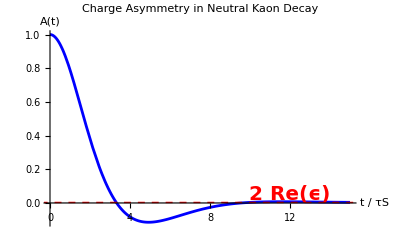

```mathematica
Plot[asymmetry[x*tauS],{x,0,15},PlotRange->All,AxesLabel->{"t / τ_S","A(t)"},PlotLabel->"Charge Asymmetry in Neutral Kaon Decay",GridLines->{None,{2*reEps}},PlotStyle->Blue,Epilog->{Red,Dashed,InfiniteLine[{0,2*reEps},{1,0}],Text[Style["2 Re(ϵ)",Red,Bold,20],{12,30*reEps}]},ImageSize->Full,LabelStyle->Directive[FontSize->20]]
```

```mathematica
asymmetry[200*tauS]
2*reEps
```

0.00323399

0.00323399